```mathematica
FullSimplify[Series[q/(4π ϵ0)/Sqrt[(r Sin[θ]-R)^2+(r Cos[θ]-R)^2],{R,Infinity,2}]]
```

q/(4 √2 π ϵ0 R)+(q r (Cos[θ]+Sin[θ]))/(8 √2 π ϵ0 R^2)+O[1/R]^3

```mathematica
Gamma[1/2]/Gamma[1]/Gamma[1/2]
```

1

```mathematica
FullSimplify[(1-Cos[x])/Sin[x]]
```

Tan[x/2]

```mathematica
Manipulate[
With[{ϵ=10^(-n)},Plot[Re[1-Cos[m θ]-Tan[m π/(4+2ϵ)]Sin[m θ]],{θ,0,π/2}]]
,{m,0,10,1},{n,2,5}
]
```

```mathematica
Series[Tan[m π/4]/R^m,{m,2,1},{R,Infinity,1}]
```

O[1/R]^2/(m-2)+O[1/R]^2+O[1/R]^2 (m-2)+O[m-2]^2

```mathematica
Series[Tan[m π/4]/R^m,{R,Infinity,1},{m,2,1}]
```

-4/((π R^2) (m-2))+(4 Log[R])/(π R^2)+((π^2-24 Log[R]^2) (m-2))/(12 π R^2)+O[m-2]^2

```mathematica
Series[Tan[m π/4]/R^m,{R,Infinity,1},{m,6,1}]
```

-4/((π R^6) (m-6))+(4 Log[R])/(π R^6)+((π^2-24 Log[R]^2) (m-6))/(12 π R^6)+O[m-6]^2

```mathematica
Series[Tan[m π/(4+2 ϵ)],{m,2,1},{ϵ,0,1}]
```

(4/(π ϵ)+2/π-(π ϵ)/12+O[ϵ]^2)+(4/(π ϵ^2)+2/(π ϵ)+π/12-(π ϵ)/24+O[ϵ]^2) (m-2)+O[m-2]^2

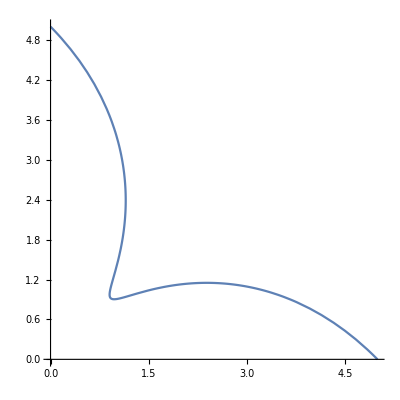

```mathematica
With[{R=5,n=3.41},PolarPlot[R Sqrt[(1-1/(1+Tan[θ]^n)^(1/n))^2+(1-Tan[θ]/(1+Tan[θ]^n)^(1/n))^2],{θ,0,π/2}]]
```

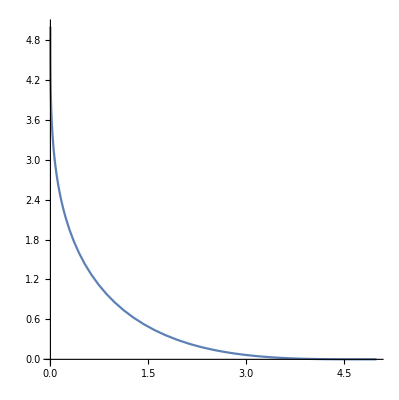

```mathematica
With[{R=5,n=3.41},ParametricPlot[{R (1-1/(1+Tan[θ]^n)^(1/n)),R(1-Tan[θ]/(1+Tan[θ]^n)^(1/n))},{θ,0,π/2}]]
```

```mathematica
Block[
{n},
n=Input[];
Print["n = ",n];
Limit[ArcTan[(1+Tan[θ]^n)^(1/n)-1,(1+Tan[θ]^n)^(1/n)-Tan[θ]],θ->π/4]
]
```

n = 4

π/4

```mathematica
Block[
{n},
n=Input[];
Print["n = ",n];
Print[Limit[ArcTan[(1+Tan[θ]^n)^(1/n)-1,(1+Tan[θ]^n)^(1/n)-Tan[θ]],θ->0]];
Print[N[π/2]];
]
```

n = 5.12

1.5708

1.5708

```mathematica
Block[
{n},
n=Input[];
Print["n = ",n];
Limit[ArcTan[(1+Cot[θ]^n)^(1/n)-Cot[θ],(1+Cot[θ]^n)^(1/n)-1],θ->π/2]
]
```

n = 8.09

0.

```mathematica
Block[
{n},
n=Input[];
Print["n = ",n];
Print[Limit[ArcTan[(1+Tan[θ]^n)^(1/n)-1,(1+Tan[θ]^n)^(1/n)-Tan[θ]],θ->π/4]];
Print[N[π/4]];
]
```

n = 4.12

0.785398

0.785398

```mathematica
Manipulate[Plot[ArcTan[(1+Tan[θ]^n)^(1/n)-1,(1+Tan[θ]^n)^(1/n)-Tan[θ]],{θ,0,π/2}],{n,2,5}]
```

```mathematica
Solve[Tan[θ]==((1+Tan[ϕ]^n)^(1/n)-Tan[ϕ])/((1+Tan[ϕ]^n)^(1/n)-1),ϕ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Tan[θ]==(-Tan[ϕ]+(1+Tan[ϕ]^n)^(1/n))/(-1+(1+Tan[ϕ]^n)^(1/n)),ϕ]

```mathematica
FullSimplify[Series[1-1/(1+ϵ)^(1/n),{n,Infinity,1},{ϵ,0,1}]]
```

(ϵ+O[ϵ]^2)/n+O[1/n]^2

```mathematica
FullSimplify[Series[1-Tan[θ]/(1+ϵ)^(1/n),{ϵ,0,1},{n,Infinity,1}]]
```

(1-Tan[θ])+(Tan[θ]/n+O[1/n]^2) ϵ+O[ϵ]^2

```mathematica
FullSimplify[Series[1-Cot[θ]/(1+ϵ)^(1/n),{ϵ,0,1},{n,Infinity,1}]]
```

(1-Cot[θ])+(Cot[θ]/n+O[1/n]^2) ϵ+O[ϵ]^2

```mathematica
Series[1-1/2^(1/n),{n,Infinity,2}]
```

Log[2]/n-Log[2]^2/(2 n^2)+O[1/n]^3

```mathematica
FullSimplify[Solve[
{r Cos[ϕ]==R Tan[θ]^n/n,r Sin[ϕ]==R(1-Tan[θ])},{r,ϕ}
]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→-(R √(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))/n,ϕ→-ArcCos[-Tan[θ]^n/(√(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))]},{r→-(R √(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))/n,ϕ→ArcCos[-Tan[θ]^n/(√(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))]},{r→(R √(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))/n,ϕ→-ArcCos[Tan[θ]^n/(√(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))]},{r→(R √(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))/n,ϕ→ArcCos[Tan[θ]^n/(√(n^2 (-1+Tan[θ])^2+Tan[θ]^(2 n)))]}}

```mathematica
FullSimplify[(1-1/(1+Tan[ξ]^n)^(1/n))^2+(1-Tan[ξ]/(1+Tan[ξ]^n)^(1/n))^2]
```

(-1+(1+Tan[ξ]^n)^(-1/n))^2+(-1+Tan[ξ] (1+Tan[ξ]^n)^(-1/n))^2

```mathematica
FullSimplify[Series[Sqrt[(1-1/(1+ϵ)^(1/n))^2+(1-Tan[ξ]/(1+ϵ)^(1/n))^2],{n,Infinity,1},{ϵ,0,1}],Assumptions->0<ξ<π/4]
```

Abs[-1+Tan[ξ]]+(Sign[1-Tan[ξ]] Tan[ξ] ϵ+O[ϵ]^2)/n+O[1/n]^2

```mathematica
Expand[Simplify[Series[ArcTan[((1+ϵ)^(1/n)-Tan[ξ])/((1+ϵ)^(1/n)-1)],{ϵ,0,1},{n,Infinity,1}],Assumptions->0<ξ<π/4&&0<Tan[ξ]≤1&&ϵ>0&&n>0]]
```

((π/(2 n)+O[1/n]^2)+O[ϵ]^2) n+((1/((-1+Tan[ξ]) n)+O[1/n]^2) ϵ+O[ϵ]^2)+O[1/n]^2

```mathematica
Expand[Simplify[Series[ArcTan[((1+ϵ)^(1/n)-Tan[ξ])/((1+ϵ)^(1/n)-1)],{n,Infinity,1},{ϵ,0,1}],Assumptions->0<ξ<π/4&&0<Tan[ξ]≤1&&ϵ>0&&n>0]]
```

Piecewise[{{-π/2+(ϵ/(-1+Tan[ξ])+O[ϵ]^2)/n+O[1/n]^2, (1+ϵ)^(1/n)<1⊻(1+ϵ)^(1/n)<Tan[ξ]}, {π/2+(ϵ/(-1+Tan[ξ])+O[ϵ]^2)/n+O[1/n]^2, True}}]

```mathematica
FullSimplify[Series[Sqrt[(1-1/(1+ϵ)^(1/n))^2+(1-Cot[ξ]/(1+ϵ)^(1/n))^2],{n,Infinity,1},{ϵ,0,1}],Assumptions->0<ξ<π/4]
```

Abs[-1+Cot[ξ]]+(Cot[ξ] Sign[1-Cot[ξ]] ϵ+O[ϵ]^2)/n+O[1/n]^2

```mathematica
FullSimplify[Series[ArcTan[((1+ϵ)^(1/n)-1)/((1+ϵ)^(1/n)-Cot[ξ])],{n,Infinity,1},{ϵ,0,1}],Assumptions->π/4<ξ<π/2&&ϵ>0&&n>0]
```

(ϵ/(1-Cot[ξ])+O[ϵ]^2)/n+O[1/n]^2

```mathematica
Series[Log[1+ϵ Cos[θ]],{ϵ,0,1}]
```

Cos[θ] ϵ+O[ϵ]^2

```mathematica
Series[(1+ϵ Cos[θ])^m,{ϵ,0,1}]
```

1+m Cos[θ] ϵ+O[ϵ]^2

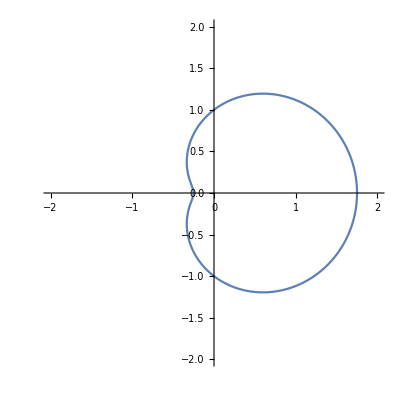

```mathematica
With[{ϵ=0.75},PolarPlot[1+ϵ Cos[θ],{θ,0,2π},PlotRange->{{-2,2},{-2,2}}]]
```

```mathematica
Series[1-Cos[m R ϵr/n/r],{r,Infinity,3}]
```

(m^2 R^2 ϵr^2)/(2 n^2 r^2)+O[1/r]^4

```mathematica
Series[Sin[m R ϵr/n/r],{r,Infinity,3}]
```

(m R ϵr)/(n r)-(m^3 R^3 ϵr^3)/(6 n^3 r^3)+O[1/r]^4

```mathematica
0.9^365
```

1.98846×10^-17

```mathematica
FullSimplify[Series[1-Cos[m(π/(2+ϵ)-R ϵr/n/r)]-Tan[m π/(4+2 ϵ)]Sin[m(π/(2+ϵ)-R ϵr/n/r)],{n,Infinity,1}]]
```

-(m R ϵr Tan[(m π)/(4+2 ϵ)])/(r n)+O[1/n]^2

```mathematica
FullSimplify[Series[Cos[m(π/(2+ϵ)-R ϵr/n/r)]+βm Sin[m(π/(2+ϵ)-R ϵr/n/r)],{n,Infinity,1}]]
```

(Cos[(m π)/(2+ϵ)]+βm Sin[(m π)/(2+ϵ)])+(m R ϵr (-βm Cos[(m π)/(2+ϵ)]+Sin[(m π)/(2+ϵ)]))/(r n)+O[1/n]^2

```mathematica
Series[Sqrt[2]R (1-1/2^(1/n)),{n,Infinity,2}]
```

(√2 R Log[2])/n-(R Log[2]^2)/(√2 n^2)+O[1/n]^3

```mathematica
N[Sqrt[2]Log[2]]
```

0.980258

```mathematica
N[1/Sqrt[2]Log[2]^2]
```

0.339732

```mathematica
Limit[1/n Log[n],n->Infinity]
```

0

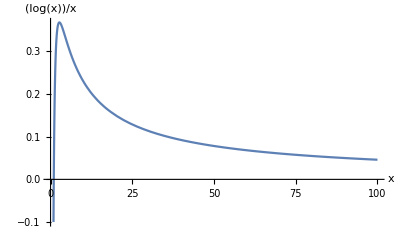

```mathematica
Plot[Log[x]/x,{x,0.01,100},AxesLabel->{Automatic,Log[x]/x}]
```

```mathematica
Binomial[5,2]
```

10

```mathematica
(Log[2]^m/2^(3m/2) Binomial[2m,m]*(1-Cos[m π/4]-Tan[m π/4]Sin[m π/4]))/.{m->1}
```

((1-√2) Log[2])/(√2)

```mathematica
Series[1/n(1-1/n Sqrt[2]Log[2])^n,{n,Infinity,2}]
```

2^(-√2)/n-(2^(-√2) Log[2]^2)/n^2+O[1/n]^3

```mathematica
N[FullSimplify[q/(8Sqrt[2]π ϵ0 R)2^(-Sqrt[2])]]
```

(0.0105566 q)/(R ϵ0)

```mathematica
N[FullSimplify[q(Sqrt[2]-1)Log[2]/(8π ϵ0 R)]]
```

(0.0114238 q)/(R ϵ0)

```mathematica
N[2^(-3.5-Sqrt[2])]
```

0.0331646

```mathematica
N[(Sqrt[2]-1)Log[2]/8]
```

0.0358889

```mathematica
0.27243/3.31646*100
```

8.21448

```mathematica
Manipulate[With[{R=5},ParametricPlot[{R (1-1/(1+Tan[θ]^n)^(1/n)),R(1-Tan[θ]/(1+Tan[θ]^n)^(1/n))},{θ,0,π/2.01}]],{n,2,10}]
```

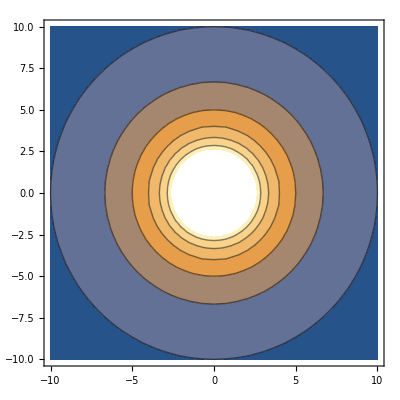

```mathematica
With[{r=10},ContourPlot[1/Sqrt[x^2+y^2],{x,-r,r},{y,-r,r}]]
```

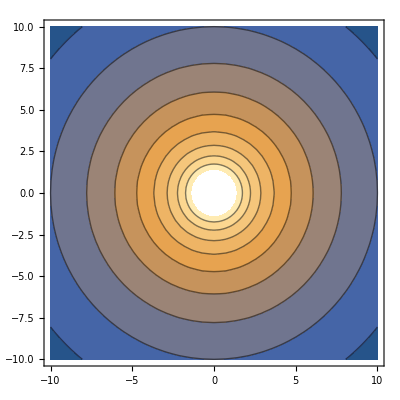

```mathematica
With[{r=10},ContourPlot[-1/2Log[(x^2+y^2)/r^2],{x,-r,r},{y,-r,r}]]
```

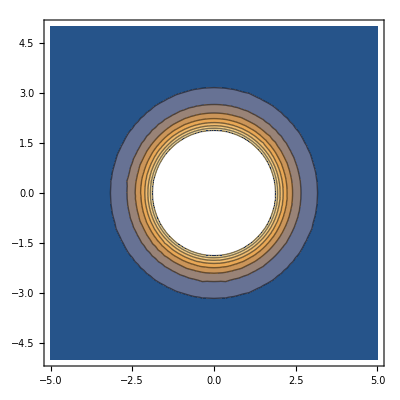

```mathematica
With[{r=5,m=4},ContourPlot[1/Sqrt[x^2+y^2]^m,{x,-r,r},{y,-r,r}]]
```

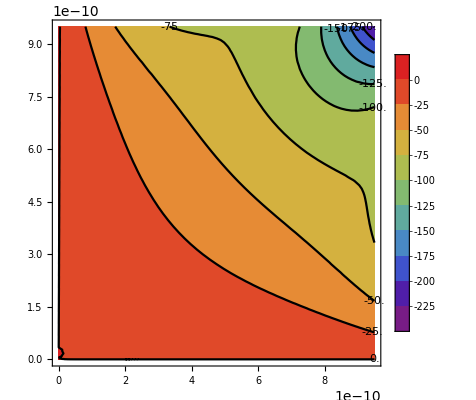

```mathematica
With[
{ϵ=5*10^(-3),R=10^(-9),q=1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=10,n=100},
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,0.95R},{y,0,0.95R},PlotTheme->"Web",ColorFunction->"Rainbow",ContourLabels->All
]
]
```

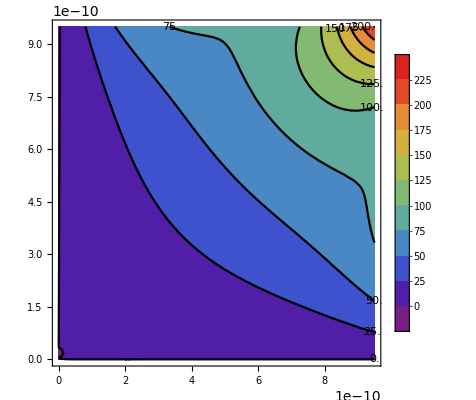

```mathematica
With[
{ϵ=5*10^(-3),R=10^(-9),q=-1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=10,n=100},
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,0.95R},{y,0,0.95R},PlotTheme->"Web",ColorFunction->"Rainbow",ContourLabels->All
]
]
```

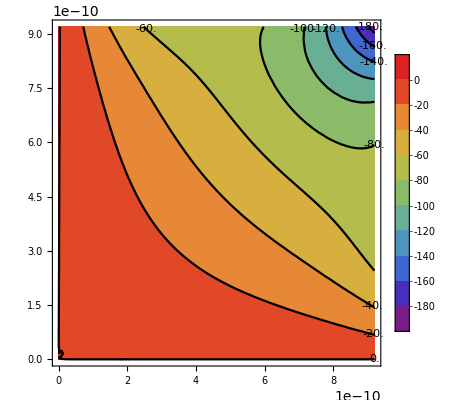

```mathematica
With[
{ϵ=5*10^(-3),R=10^(-9),q=1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=10,n=120},
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,0.92R},{y,0,0.92R},PlotTheme->"Web",ColorFunction->"Rainbow",ContourLabels->All
]
]
```

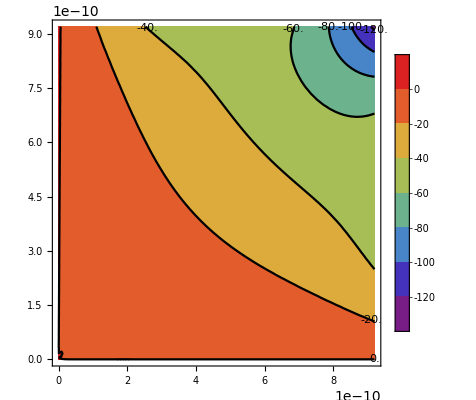

```mathematica
With[
{ϵ=7.5*10^(-3),R=10^(-9),q=1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=10,n=120},
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,0.92R},{y,0,0.92R},PlotTheme->"Web",ColorFunction->"Rainbow",ContourLabels->All
]
]
```

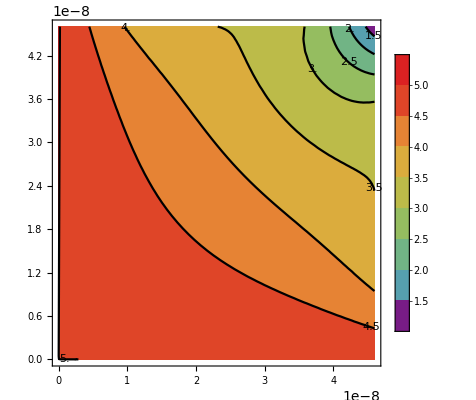

```mathematica
With[
{ϵ=5*10^(-3),R=5*10^(-8),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=10,n=500},
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,0.92R},{y,0,0.92R},PlotTheme->"Web",ColorFunction->"Rainbow",ContourLabels->All
]
]
```

```mathematica
-D[1/n(1-r/R)^n,r]
```

(1-r/R)^(-1+n)/R

```mathematica
-D[1/n(1-r/R)^n(r/R)^m,r]
```

-(m (1-r/R)^n (r/R)^(-1+m))/(n R)+((1-r/R)^(-1+n) (r/R)^m)/R

```mathematica
-D[1-Cos[m θ]-Tan[m π/(4+2ϵ)]Sin[m θ],θ]
```

-m Sin[m θ]+m Cos[m θ] Tan[(m π)/(4+2 ϵ)]

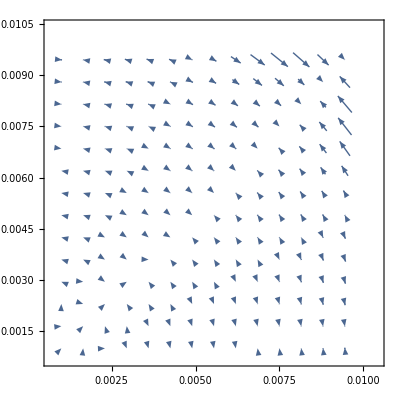

```mathematica
With[
{ϵ=5*10^(-4),R=10^(-2),q=1.6*10^(-19),ϵ0=8.85*10^(-12),M=10,n=100},
VectorPlot[If[
0≤ArcTan[x,y]<π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]))}],
If[ArcTan[x,y]==π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]))}],
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]))}]]
],{x,0.1R,1.01R},{y,0.1R,1.01R},VectorScale->{0.05,1,Automatic}
]
]
```

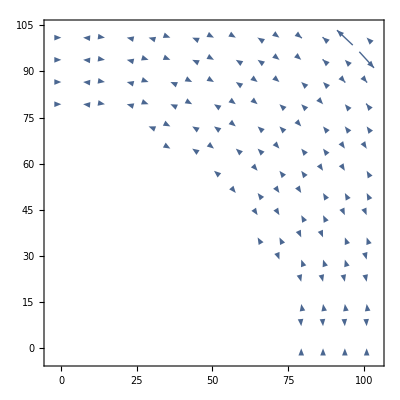

```mathematica
With[
{ϵ=5*10^(-5),R=10^(2),q=1.6*10^(-19),ϵ0=8.85*10^(-12),M=40,n=150},
VectorPlot[If[
0≤ArcTan[x,y]<π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]))}],
If[ArcTan[x,y]==π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]))}],
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]))}]]
],{x,0R,1.01R},{y,0R,1.01R},VectorScale->{0.05,1,Automatic}
]
]
```

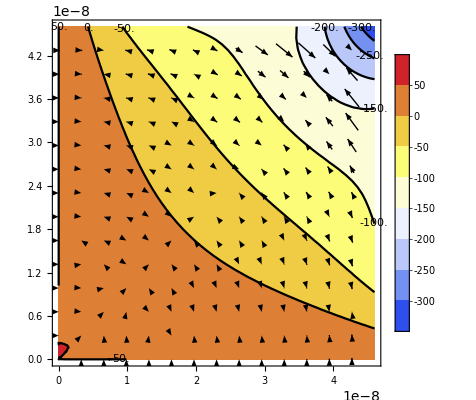

```mathematica
With[
{ϵ=5*10^(-5),R=5*10^(-8),q=1.6*10^(-19),ϕ0=50,ϵ0=8.85*10^(-12),M=10,n=150},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,0.92R},{y,0,0.92R},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[If[
0≤ArcTan[x,y]<π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]))}],
If[ArcTan[x,y]==π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]))}],
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]))}]]
],{x,0R,0.92R},{y,0R,0.92R},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

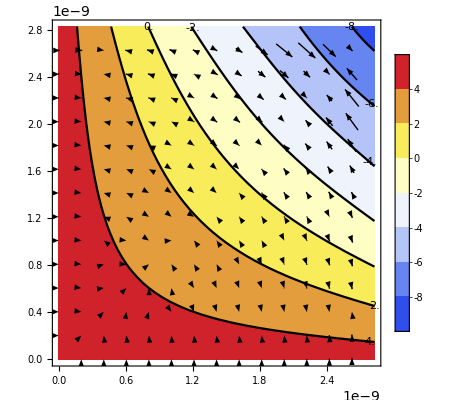

```mathematica
With[
{ϵ=7.5*10^(-3),R=4*10^(-9),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=10,n=200},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[If[
0≤ArcTan[x,y]<π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]))}],
If[ArcTan[x,y]==π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]))}],
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]))}]]
],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

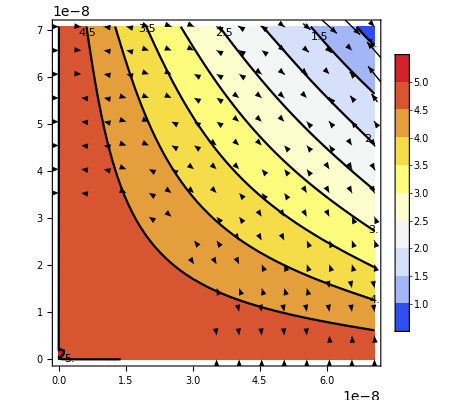

```mathematica
With[
{ϵ=10^(-3),R=10^(-7),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=20,n=200},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[If[
0≤ArcTan[x,y]<π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]],{m,1,M}]))}],
If[ArcTan[x,y]==π/4,
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]))}],
N[
{1/Sqrt[x^2+y^2](x(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}]
)-y(
q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]
)),1/Sqrt[x^2+y^2](y(q/(16Sqrt[2]π ϵ0 R^2)Sum[(Sqrt[x^2+y^2]/4/R)^(m-1)Binomial[2m,m]m(Cos[m ArcTan[x,y]]+Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]-1),{m,1,M}]+q/(8 Sqrt[2]π ϵ0 R^2)(1-Sqrt[x^2+y^2]/R)^(n-1)+q/(4Sqrt[2]π ϵ0 R^2)Sum[(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[x,y]]((Sqrt[x^2+y^2]/R)^m(1-Sqrt[x^2+y^2]/R)^(n-1)-m/n(Sqrt[x^2+y^2]/R)^(m-1)(1-Sqrt[x^2+y^2]/R)^n)Sec[m π/(2+ϵ)],{m,1,M}])+x(q/(16Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m Binomial[2m,m](Cos[m ArcTan[x,y]]Tan[m π/(4+2ϵ)]-Sin[m ArcTan[x,y]]),{m,1,M}]-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4Sqrt[2]π ϵ0 R^2) Sum[(Sqrt[x^2+y^2]/R)^(m-1)m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sin[m ArcTan[x,y]]Sec[m π/(2+ϵ)],{m,1,M}]))}]]
],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

```mathematica
FullSimplify[-D[(x^2+y^2)^(m/2)/(4R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[m π/(4+2ϵ)]Sin[m ArcTan[y/x]]),x]]
```

4^-m m R^-m (x^2+y^2)^(-1+m/2) Binomial[2 m,m] (-x+Sin[m ArcTan[y/x]] (y+x Tan[(m π)/(4+2 ϵ)])+Cos[m ArcTan[y/x]] (x-y Tan[(m π)/(4+2 ϵ)]))

```mathematica
FullSimplify[-D[(x^2+y^2)^(m/2)/(4R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[m π/(4+2ϵ)]Sin[m ArcTan[y/x]]),y]]
```

4^-m m R^-m (x^2+y^2)^(-1+m/2) Binomial[2 m,m] (-y+Cos[m ArcTan[y/x]] (y+x Tan[(m π)/(4+2 ϵ)])+Sin[m ArcTan[y/x]] (-x+y Tan[(m π)/(4+2 ϵ)]))

```mathematica
FullSimplify[-D[1/2/n(1-Sqrt[x^2+y^2]/R)^n,x]]
```

(x (1-(√(x^2+y^2))/R)^(-1+n))/(2 R √(x^2+y^2))

```mathematica
Simplify[-D[1/n(1-Sqrt[x^2+y^2]/R)^n(Sqrt[x^2+y^2]^m/R^m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[y/x]]),x]]
```

1/(n (-R+√(x^2+y^2)))4^(-1-m) (1+m) R^-m (x^2+y^2)^(1/2 (-3+m)) (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (-x (n (x^2+y^2)+m (x^2+y^2-R √(x^2+y^2))) Cos[m ArcTan[y/x]]-m y (x^2+y^2-R √(x^2+y^2)) Sin[m ArcTan[y/x]]) Tan[((1+m) π)/(4+2 ϵ)]

```mathematica
FullSimplify[-D[1/2/n(1-Sqrt[x^2+y^2]/R)^n,y]]
```

(y (1-(√(x^2+y^2))/R)^(-1+n))/(2 R √(x^2+y^2))

```mathematica
Simplify[-D[1/n(1-Sqrt[x^2+y^2]/R)^n(Sqrt[x^2+y^2]^m/R^m(m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Cos[m ArcTan[y/x]]),y]]
```

-1/(n (-R+√(x^2+y^2)))4^(-1-m) (1+m) R^-m (x^2+y^2)^(1/2 (-3+m)) (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (y (n (x^2+y^2)+m (x^2+y^2-R √(x^2+y^2))) Cos[m ArcTan[y/x]]-m x (x^2+y^2-R √(x^2+y^2)) Sin[m ArcTan[y/x]]) Tan[((1+m) π)/(4+2 ϵ)]

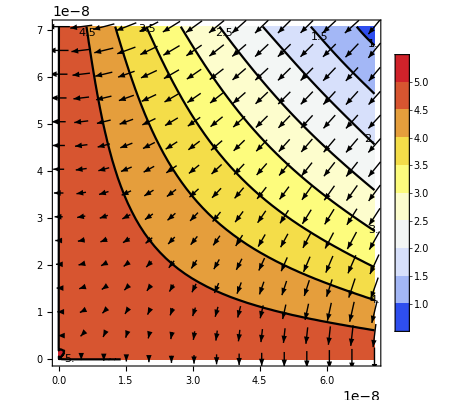

```mathematica
With[
{ϵ=10^(-3),R=10^(-7),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=20,n=200},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
(-1)*{
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[m π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[m π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

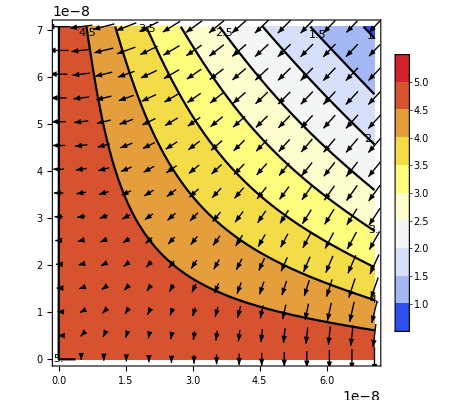

```mathematica
With[
{ϵ=10^(-3),R=10^(-7),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=150,n=720},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
(-1)*{
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

```mathematica
Integrate[1/ϵ Exp[x/ϵ],x]
```

ⅇ^(x/ϵ)

```mathematica
Series[c2 Exp[-x/ϵ]+Exp[-x/ϵ]/ϵ Integrate[h[x]Exp[x/ϵ],x]+c1,{ϵ,0,1}]
```

c1+c2 ⅇ^(-x/ϵ+O[ϵ]^2)+ⅇ^(-x/ϵ+O[ϵ]^2) (∫ⅇ^(x/ϵ+O[ϵ]^2) h[x]ⅆx) (1/ϵ+O[ϵ]^2)

```mathematica
Limit[Exp[x/ϵ],ϵ->0,Direction->-1]
```

ConditionalExpression[∞,x>0]

```mathematica
Solve[{c1+c2==0,c1+c2 Exp[-1/ϵ]==-I1},{c1,c2}]
```

{{c1→-(ⅇ^(1/ϵ) I1)/(-1+ⅇ^(1/ϵ)),c2→(ⅇ^(1/ϵ) I1)/(-1+ⅇ^(1/ϵ))}}

```mathematica
Series[A Sin[ϵ x]+B Cos[ϵ x],{ϵ,0,4}]
```

B+A x ϵ-1/2 (B x^2) ϵ^2-1/6 (A x^3) ϵ^3+1/24 B x^4 ϵ^4+O[ϵ]^5

```mathematica
Limit[A Sin[ϵ x]/ϵ,ϵ->0]
```

A x

```mathematica
Integrate[1/Sqrt[x],x]
```

2 √x

```mathematica
D[Exp[2(1-Sqrt[x])],{x,2}]
```

ⅇ^(2 (1-√x))/(2 x^(3/2))+ⅇ^(2 (1-√x))/x

```mathematica
D[Exp[2(1-Sqrt[x])],{x,1}]
```

-ⅇ^(2 (1-√x))/(√x)

```mathematica
FullSimplify[DSolve[Sqrt[x]D[f[x],x]+f[x]+Exp[2(1-Sqrt[x])]/2/x^(3/2)(1+2 x^(1/2))==0,f[x],x]]
```

{{f[x]→(ⅇ^(-2 √x) (ⅇ^2 (1+4 √x)+2 x C[1]))/(2 x)}}

```mathematica
Series[Exp[2(1-Sqrt[x])]+ϵ((ⅇ^(-2 √x) (ⅇ^2 (1+4 √x)+2 x C[1]))/(2 x)),{x,0,1}]
```

(ⅇ^2 ϵ)/(2 x)+(ⅇ^2 ϵ)/(√x)+(ⅇ^2-3 ⅇ^2 ϵ+ϵ C[1])+(-2 ⅇ^2+(10 ⅇ^2 ϵ)/3-2 ϵ C[1]) √x+(2 ⅇ^2-(7 ⅇ^2 ϵ)/3+2 ϵ C[1]) x+O[x]^(3/2)

```mathematica
Solve[(ⅇ^2-3 ⅇ^2 ϵ+ϵ C[1])==0,C[1]]
```

{{C[1]→(-ⅇ^2+3 ⅇ^2 ϵ)/ϵ}}

```mathematica
FullSimplify[(Exp[2(1-Sqrt[x])]+Exp[2(1-Sqrt[x])]x(3η x-1)+η/2Exp[2(1-Sqrt[x])](1+4Sqrt[x]))/.{x->0}]
```

1/2 ⅇ^2 (2+η)

```mathematica
FullSimplify[(Exp[2(1-Sqrt[x])]+Exp[2(1-Sqrt[x])]x(3η x-1)+η/2Exp[2(1-Sqrt[x])](1+4Sqrt[x]))/.{x->1}]
```

(11 η)/2

```mathematica
Limit[Exp[-x/ϵ],ϵ->0,Direction->"FromAbove",Assumptions->x>0]
```

0

```mathematica
Series[(1-4ϵ)^(1/2),{ϵ,0,2}]
```

1-2 ϵ-2 ϵ^2+O[ϵ]^3

```mathematica
Solve[{A+B==0,A E^(-1)+B E^(-1/ϵ)==1},{A,B}]
```

{{A→ⅇ^(1+1/ϵ)/(-ⅇ+ⅇ^(1/ϵ)),B→-ⅇ^(1+1/ϵ)/(-ⅇ+ⅇ^(1/ϵ))}}

```mathematica
Series[Exp[-x/ϵ],{ϵ,0,1},Assumptions->ϵ>0&&x>0]
```

ⅇ^(-x/ϵ+O[ϵ]^2)

```mathematica
Limit[Exp[-x/ϵ],ϵ->0,Direction->"FromAbove",Assumptions->x>0]
```

0

```mathematica
DSolve[D[f[x],x,x]+f'[x]==0,f[x],x]
```

{{f[x]→-ⅇ^-x C[1]+C[2]}}

```mathematica
Limit[Exp[-1/x],x->0,Direction->"FromAbove"]
```

0

```mathematica
Limit[1-Exp[-1/ϵ],ϵ->0,Direction->"FromAbove"]
```

1

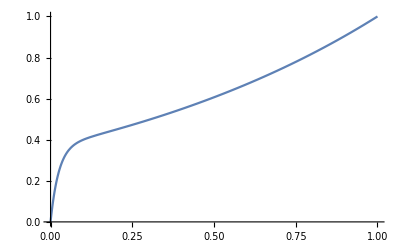

```mathematica
With[
{ϵ=1/40},
Plot[1/E(Exp[x]-Exp[-x/ϵ]),{x,0,1},AxesOrigin->{0,0}]
]
```

```mathematica
FullSimplify[(ϵ D[y,{x,2}]+D[y,x]-y)/.{y->1/E(Exp[x]-Exp[-x/ϵ])}]
```

(-ⅇ^x+ⅇ^(-x/ϵ))/ⅇ

```mathematica
FullSimplify[ϵ D[1/E(Exp[x]-Exp[-x/ϵ]),{x,2}]+D[1/E(Exp[x]-Exp[-x/ϵ]),x]-(1/E(Exp[x]-Exp[-x/ϵ]))]
```

(ⅇ^(-x/ϵ)+ⅇ^x ϵ)/ⅇ

```mathematica
With[
{ϵ=10^(-12)},
Mean[Table[(ⅇ^(-x/ϵ)+ⅇ^x ϵ)/ⅇ,{x,0,1,10^(-5)}]]//N
]
```

3.67876×10^-6

```mathematica
DSolve[D[f[x],x,x]+2f'[x]==0,f[x],x]
```

{{f[x]→-1/2 ⅇ^(-2 x) C[1]+C[2]}}

```mathematica
D[B/2(E^(-2)-E^(-2x)),x]
```

B ⅇ^(-2 x)

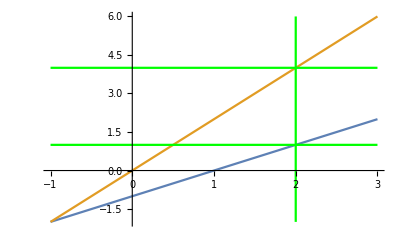

```mathematica
Show[Plot[{m-1,2m},{m,-1,3}],ParametricPlot[{x,1},{x,-1,3},PlotStyle->Green],ParametricPlot[{x,4},{x,-1,3},PlotStyle->Green],ParametricPlot[{2,x},{x,-2,6},PlotStyle->Green]]
```

```mathematica
{m+1,2m}/.{m->-2}
```

{-1,-4}

```mathematica
FullSimplify[(c1-ρ/ϵ^3)/.{ρ->ϵ^2 x}]
```

c1-x/ϵ

```mathematica
DSolve[D[u[x],x,x]+ϵ^2 u[x]u'[x]==0,u[x],x]
```

{{u[x]→(√2 √C[1] Tanh[1/2 (√2 x ϵ √C[1]+√2 ϵ √C[1] C[2])])/ϵ}}

```mathematica
FullSimplify[Series[(√2 √C[1] Tanh[1/2 (√2 x ϵ √C[1]+√2 ϵ √C[1] C[2])])/ϵ,{ϵ,0,3}]]
```

C[1] (x+C[2])-1/6 (C[1]^2 (x+C[2])^3) ϵ^2+O[ϵ]^4

```mathematica
Limit[(√2 √C[1] Tanh[1/2 (√2 x ϵ √C[1]+√2 ϵ √C[1] C[2])])/ϵ,ϵ->0]
```

C[1] (x+C[2])

```mathematica
Limit[(1-x)^n/n,n->Infinity]
```

ConditionalExpression[0,Log[1-x]<0]

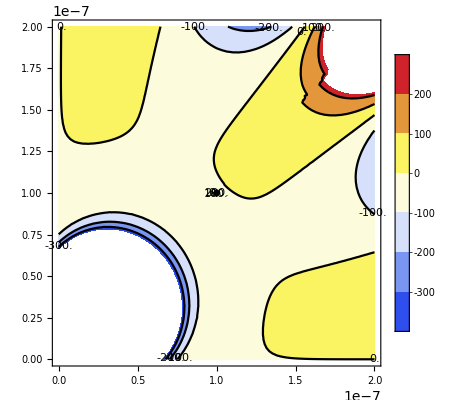

```mathematica
With[
{ϵ=10^(-2),ϵ1=10^(-4),R=10^(-7),q=-1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=10,n=6},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+q/(4π ϵ0 Sqrt[x^2+y^2])Sum[Binomial[2m,m](R(x+y)/2/(x^2+y^2))^(m),{m,0,M}]-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])+
If[0≤ArcTan[y/x]<π/4,1/n(Abs[1-Sqrt[(x^2+y^2)/R^2]])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(Abs[1-Sqrt[(x^2+y^2)/R^2]])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,ϵ1 R,2R},{y,ϵ1 R,2R},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
]
]
]
```

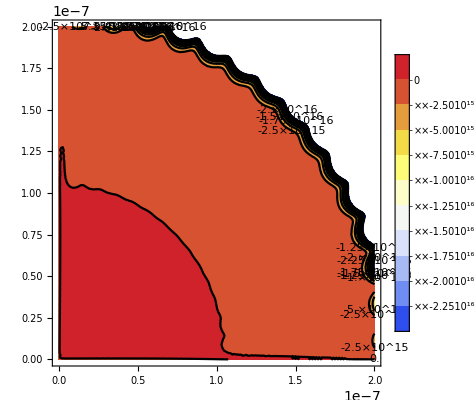

```mathematica
With[
{ϵ=10^(-2),ϵ1=10^(-4),R=10^(-7),q=-1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=60,n=100},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)+
If[0≤ArcTan[y/x]<π/4,1/n(Abs[1-Sqrt[(x^2+y^2)/R^2]])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(Abs[1-Sqrt[(x^2+y^2)/R^2]])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,ϵ1 R,2R},{y,ϵ1 R,2R},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
]
]
]
```

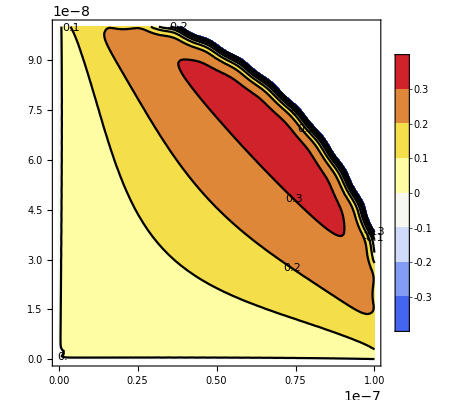

```mathematica
With[
{ϵ=10^(-2),ϵ1=10^(-4),R=10^(-7),q=-1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=60,n=100},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)+
If[0≤ArcTan[y/x]<π/4,1/n(Abs[1-Sqrt[(x^2+y^2)/R^2]])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(Abs[1-Sqrt[(x^2+y^2)/R^2]])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,ϵ1 R,R/Sqrt[1]},{y,ϵ1 R,R/Sqrt[1]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
]
]
]
```

```mathematica
D[-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2]),x]
```

(q (-R+x))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)

```mathematica
D[-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2]),y]
```

(q (-R+y))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)

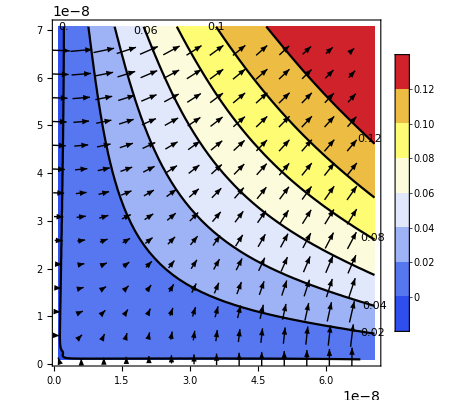

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
-N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.01 R,R/Sqrt[2]},{y,0.01 R,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
(-1){
(-q (-R+x))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)-q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]-
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(-q (-R+y))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)-q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]-q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.01 R,R/Sqrt[2]},{y,0.01 R,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

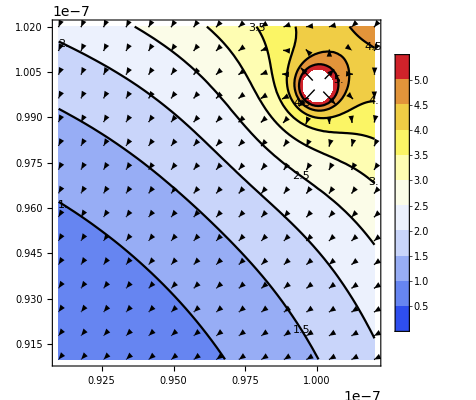

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.91R,1.02R},{y,0.91R,1.02R},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
{
(q (-R+x))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(q (-R+y))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.91R,1.02R},{y,0.91R,1.02R},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

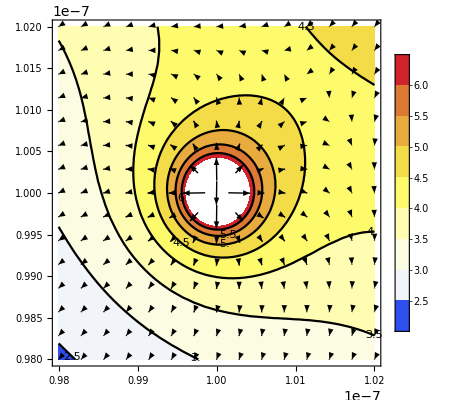

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=1.6*10^(-19),ϕ0=0,ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.98R,1.02R},{y,0.98R,1.02R},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
{
(q (-R+x))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(q (-R+y))/(4 π ((-R+x)^2+(-R+y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(Abs[1-Sqrt[x^2+y^2]/R])^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(Abs[1-Sqrt[x^2+y^2]/R])^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.98R,1.02R},{y,0.98R,1.02R},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

```mathematica
(** Final model **)
```

```mathematica
FullSimplify[D[-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2]),x]]
```

(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)

```mathematica
FullSimplify[D[-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2]),y]]
```

(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)

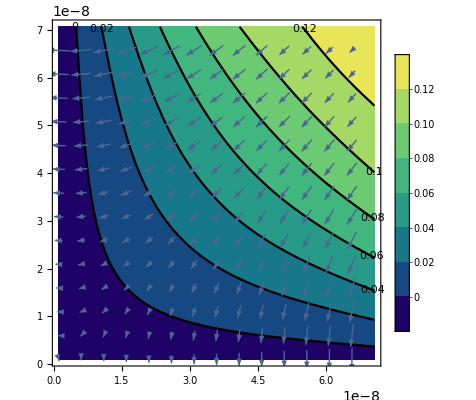

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=-1.6*10^(-19),ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
N[q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.01R,R/Sqrt[2]},{y,0.01R,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[
{
(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.01R,R/Sqrt[2]},{y,0.01R,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic
]
]
]
```

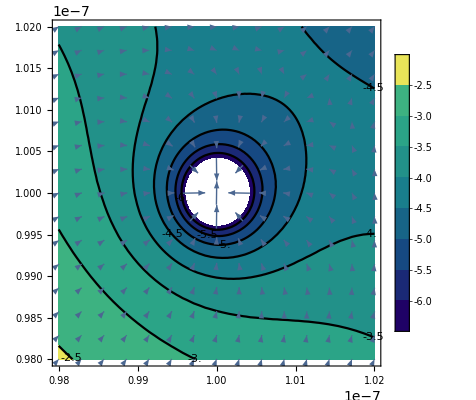

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=-1.6*10^(-19),ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
N[q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.98R,1.02R},{y,0.98R,1.02R},PlotTheme->"Web",ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[
{
(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.98R,1.02R},{y,0.98R,1.02R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic
]
]
]
```

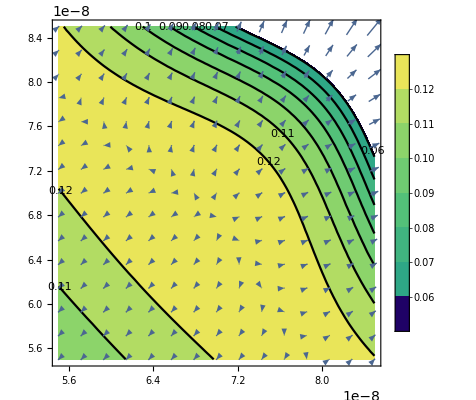

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=-1.6*10^(-19),ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
N[q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.55R,0.85R},{y,0.55R,0.85R},PlotTheme->"Web",ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[
{
(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.55R,0.85R},{y,0.55R,0.85R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic
]
]
]
```

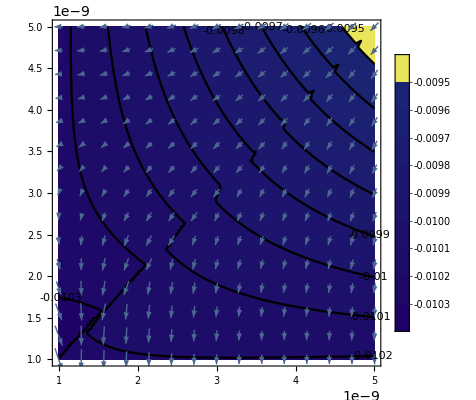

```mathematica
With[
{ϵ=2.1*10^(-2),R=10^(-7),q=-1.6*10^(-19),ϵ0=8.85*10^(-12),M=20,n=100},
Show[
ContourPlot[
N[q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0.01R,0.05R},{y,0.01R,0.05R},PlotTheme->"Web",ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[
{
(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0.01R,0.05R},{y,0.01R,0.05R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic
]
]
]
```

```mathematica
FullSimplify[(ω0 (1-2(f)^2)+2D1 D[f,x]^2-D[f,t])/.{f->Sin[x]Sin[t]}]
```

ω0-2 ω0 Sin[t]^2 Sin[x]^2

```mathematica
FullSimplify[(ω0 (1-2(f)^2)+2D1 D[f,x]^2-D[f,t])/.{f->1/4 Exp[Sqrt[ω0/D1](x-x0[t])]+1/2Exp[Sqrt[ω0/D1](x0[t]-x)]}]
```

-1/8 ω0 (Cosh[√(ω0/D1) (x-x0[t])]-3 Sinh[√(ω0/D1) (x-x0[t])])^2

```mathematica
Block[
{ω0,D1,f,x0,x,t},
f[x_,t_]:=1/4 Exp[Sqrt[ω0/D1](x-x0[t])]+1/2Exp[Sqrt[ω0/D1](x0[t]-x)];
FullSimplify[(ω0 (1-2(f[x,t])^2)+2D1 D[f[x,t],x]^2-D[f[x,t],t])]
]
```

-1/4 √(ω0/D1) (Cosh[√(ω0/D1) (x-x0[t])]-3 Sinh[√(ω0/D1) (x-x0[t])]) x0'[t]